```mathematica
xa[k_]:=Quiet[NIntegrate[(k^3*Sqrt[1+y^4])/(y^2*Sqrt[y^6-k^6]),{y,k,yy}]]
```

```mathematica
xavsuatb1={};
xavsuatb2={};
xavsuatb4={};
With[{k=1},For[i=0,i<=3.5,i+=0.01,yy=k*10^i;
xa1=xa[k];
AppendTo[xavsuatb1,{yy,xa1}];
]];
With[{k=0.25},For[i=0,i<=3.25,i+=0.01,yy=k*10^i;
xa2=xa[k];
AppendTo[xavsuatb2,{yy,xa2}];
]];
With[{k=4},For[i=0,i<=3,i+=0.01,yy=k*10^i;
xa4=xa[k];
AppendTo[xavsuatb4,{yy,xa4}];
]];
```

```mathematica
xavsuatb1v2=Join[Reverse[xavsuatb1],Transpose[{xavsuatb1[[All,1]],-xavsuatb1[[All,2]]}]];
xavsuatb2v2=Join[Reverse[xavsuatb2],Transpose[{xavsuatb2[[All,1]],-xavsuatb2[[All,2]]}]];
xavsuatb4v2=Join[Reverse[xavsuatb4],Transpose[{xavsuatb4[[All,1]],-xavsuatb4[[All,2]]}]];
```

```mathematica
ListLinePlot[{xavsuatb1v2,xavsuatb2v2,xavsuatb4v2},ScalingFunctions->{"Log"}, AxesLabel->{"au","x/a"},PlotLabels->{"au_c=1","au_c=1/4","au_c=4"}]
```

-Graphics-

```mathematica
loveravsauctb={};
crvfittb={};
For[i=0.01,i≤3,i+=0.01,k=2^i-.93;
l=2*Quiet[NIntegrate[(k^3*Sqrt[1+y^4])/(y^2*Sqrt[y^6-k^6]),{y,k,Infinity}]];
curvefit=1.4061326930120044-1.4569696199483422 Cos[k]+0.8635013288743747 Csc[k];
AppendTo[loveravsauctb,{k,l}];
AppendTo[crvfittb,{k,curvefit}]
]
```

```mathematica
ListLinePlot[{loveravsauctb,crvfittb},PlotRange->{{0,2},{1,8}},AxesLabel->{"au_c","l/a"},ImageSize->Large,PlotLabels->{"Actual","Curve Fit"}]
```

-Graphics-

```mathematica
lavsauctb2 = {};
aucvslatb={};
For[i=0.00001,i≤0.81,i+=0.001,k=i;
l=2*Quiet[NIntegrate[(k^3*Sqrt[1+y^4])/(y^2*Sqrt[y^6-k^6]),{y,k,Infinity}]];
AppendTo[lavsauctb2,{k,l}];
AppendTo[aucvslatb,{l,k}]
]
```

```mathematica
Clear[la]
aucvsla=Interpolation[aucvslatb]
```

InterpolatingFunction[…]

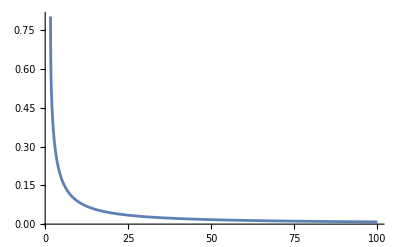

```mathematica
Plot[aucvsla[la],{la,1.61395,100},PlotRange->All]
```

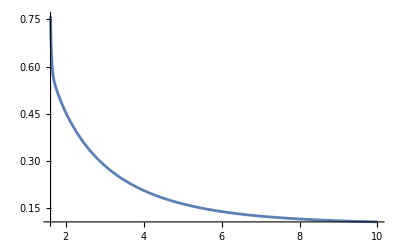

```mathematica
(*Plot[0.1+.5655916115040078` 2.628274447764749^(-0.8368292374072324 (-1.5+la)^0.789778935536507)+6.283263640208521*^19 2.7^(-2.1011131874314306 (1.490577846330067+la)^2.7542733155006793) la Log[la],{la,1.61,10},PlotRange->All]
this was not nearly as good as the interpolation function*)
```

```mathematica
adiv=Integrate[u*Sqrt[1+a^4 u^4],{u,0,ub}]
```

ConditionalExpression[(a^2 ub^2 √(1+a^4 ub^4)+ArcSinh[a^2 ub^2])/(4 a^2), ((1+ⅈ)/(a ub)∉ℝ||Re[(-1)^(1/4)/(a ub)]<-1||Re[(-1)^(1/4)/(a ub)]>1)&&(-(1-ⅈ)/(a ub)∉ℝ||Re[(-1)^(3/4)/(a ub)]<-1||Re[(-1)^(3/4)/(a ub)]>1)]

```mathematica
FullSimplify[Series[adiv,{ub,Infinity,4}]]
```

ConditionalExpression[Piecewise[{{(a^2 ub^4)/4+(1+Log[4 a^4 ub^4])/(8 a^2)+1/(32 a^6 ub^4)+O[1/ub]^5, (a|1/ub)∈ℝ&&(ub (ub+Re[(-1)^(1/4)/a])<0||Re[(-1)^(1/4)/a]/ub>1||(1+ⅈ)/a∉ℝ)&&(ub (ub+Re[(-1)^(3/4)/a])<0||Re[(-1)^(3/4)/a]/ub>1||-(1-ⅈ)/a∉ℝ)}, {1/4 √(a^4) ub^4+(1+Log[4 a^4 ub^4])/(8 √(a^4))+1/(32 (a^4)^(3/2) ub^4)+O[1/ub]^5, True}}], ]

```mathematica
alpha=90;
spvslatb2={};
(*ktb2={};
latb2={};
sdiv2tb={};*)
For[i=0.1,i≤0.799,i+=0.01,k=i+0.01;
la=2*Quiet[NIntegrate[(k^3*Sqrt[1+y^4])/(y^2*Sqrt[y^6-k^6]),{y,k,alpha}]];
sp = 2*(Quiet[NIntegrate[y*Sqrt[(1+y^4)/(1-k^6/y^6)],{y,k,alpha}]]-((alpha)^4/4+Log[alpha]/2));
(*sp2 =2*(Quiet[NIntegrate[k^2/(3(1-z^2)^(5/3))*Sqrt[(1-z^2)^(2/3)+k^4],{z,0,Sqrt[1-k^6/alpha^6]}]]-((alpha)^4/4+Log[alpha]/2)); 
sdiv=2*SetPrecision[Quiet[NIntegrate[y*Sqrt[(1+y^4)/(1-k^6/y^6)],{y,k,alpha}]],15];
sdiv2=2*SetPrecision[Quiet[NIntegrate[k^2/((1-z^2)^(5/3))*Sqrt[(1-z^2)^(2/3)+k^4],{z,0,Sqrt[1-k^6/alpha^6]}]],15];*);
AppendTo[spvslatb2,{la,sp}];
(*AppendTo[latb2,{k,la}];
AppendTo[ktb2,{la,sp2,k}];
AppendTo[sdiv2tb,{k,sdiv2}];*)
]
```

```mathematica
spvslatb2
```

{{7.84377,0.85584},{7.19151,0.848997},{6.63991,0.841839},{6.16745,0.834378},{5.75833,0.826628},{5.40071,0.818601},{5.08553,0.810309},{4.80577,0.801764},{4.55586,0.792978},{4.33134,0.783963},{4.12864,0.77473},{3.9448,0.765291},{3.77738,0.755656},{3.62437,0.745836},{3.48407,0.735841},{3.35502,0.725682},{3.23602,0.715367},{3.126,0.704908},{3.02405,0.694312},{2.92941,0.68359},{2.84137,0.672748},{2.75935,0.661797},{2.68281,0.650743},{2.61129,0.639596},{2.54438,0.628361},{2.48172,0.617047},{2.42297,0.60566},{2.36785,0.594207},{2.3161,0.582695},{2.26747,0.571129},{2.22176,0.559516},{2.17877,0.547862},{2.13832,0.536171},{2.10025,0.524449},{2.06443,0.5127},{2.03071,0.500931},{1.99898,0.489145},{1.96912,0.477347},{1.94102,0.46554},{1.9146,0.45373},{1.88976,0.441919},{1.86642,0.430112},{1.84452,0.418312},{1.82396,0.406522},{1.8047,0.394746},{1.78667,0.382987},{1.7698,0.371247},{1.75406,0.359531},{1.73939,0.347839},{1.72574,0.336175},{1.71306,0.324542},{1.70132,0.312942},{1.69048,0.301377},{1.6805,0.28985},{1.67134,0.278363},{1.66297,0.266917},{1.65536,0.255516},{1.64849,0.244161},{1.64231,0.232853},{1.63681,0.221596},{1.63196,0.21039},{1.62773,0.199238},{1.62411,0.188141},{1.62106,0.177101},{1.61857,0.16612},{1.61663,0.1552},{1.61519,0.144342},{1.61426,0.133548},{1.61382,0.122819},{1.61383,0.112158}}

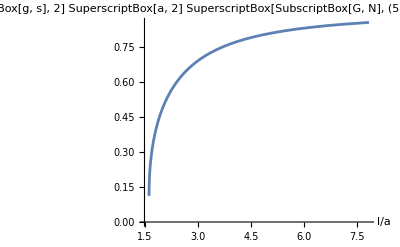

```mathematica
ListLinePlot[spvslatb2,PlotRange->Full,AxesLabel->{"l/a","(2 SuperscriptBox[SubscriptBox[g, s], 2] SuperscriptBox[a, 2] SuperscriptBox[SubscriptBox[G, N], (5)])/L^2S_A"}]
```

```mathematica
(*finally got the right shape by not being stupid and rechecking my assumptions. been trying to think of a good way to plot the mutual information in terms of different strip widths. want to find a good inverse function of la(auc), but is not working great*)
```

```mathematica
alpha=100;
spvslatb={};
spvsxatb={};
spvs2lxatb={};
mutinftb={};
For[(*i=1.61395,i<20,i+=0.1,*)
i=0,i<0.8,i+=0.05,
la=4;
xa=i*la;
k=aucvsla[la];
kx=aucvsla[xa];
k2lx=aucvsla[2*la+xa];
spl = 2*(Quiet[NIntegrate[y*Sqrt[(1+y^4)/(1-k^6/y^6)],{y,k,alpha}]]-((alpha)^4/4+Log[alpha]/2));
spx=2*(Quiet[NIntegrate[y*Sqrt[(1+y^4)/(1-kx^6/y^6)],{y,kx,alpha}]]-((alpha)^4/4+Log[alpha]/2));
sp2lx=2*(Quiet[NIntegrate[y*Sqrt[(1+y^4)/(1-k2lx^6/y^6)],{y,k2lx,alpha}]]-((alpha)^4/4+Log[alpha]/2));
mutinf=2*spl-spx-sp2lx;
AppendTo[spvslatb,{xa,spl}];
AppendTo[spvsxatb,{xa,spx}];
AppendTo[spvs2lxatb,{xa,sp2lx}];
AppendTo[mutinftb,{xa,mutinf}];
]
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.2} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.4} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

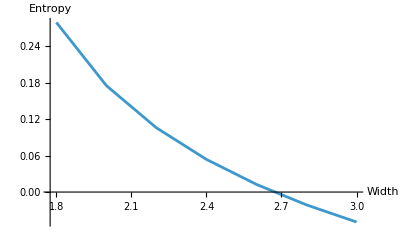

```mathematica
ListLinePlot[{mutinftb},PlotRange->Full,AxesLabel->{"Width","Entropy"}]
```

```mathematica
(*just checked how what typa results we get comparing this spvsla to the other guy, and its perfect as far as i can tell. will be getting the k values from this interpolation function for the mutual information*)
```

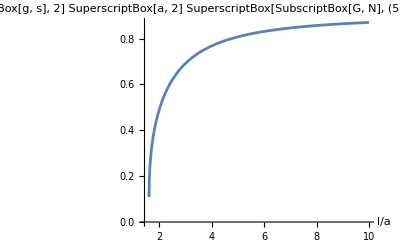

```mathematica
(*this is the sanity check*)ListLinePlot[spvslatb,PlotRange->Full,AxesLabel->{"l/a","(2 SuperscriptBox[SubscriptBox[g, s], 2] SuperscriptBox[a, 2] SuperscriptBox[SubscriptBox[G, N], (5)])/L^2S_A"}]
```

```mathematica
(*ok so the paper varies a directly instead of alpha, so lets try and do this but with all them parameters - what if i can just do the integrals in unitless params and then plot w normal guys?*)
```

```mathematica
a=1;
alpha=100;
ub=alpha/a;
spvsltb2={};
spvsxtb2={};
spvs2lxtb2={};
mutinftb2={};
For[i=0,i<0.66,i+=0.01,
la=4;
l=la*a;
xa=i*la;
x=xa*a;
k=aucvsla[la];
uc=k/a;
kx=aucvsla[xa];
ucx=kx/a;
k2lx=aucvsla[2*la+xa];
uc2lx=k2lx/a;
spl2int=2*Quiet[NIntegrate[u*Sqrt[(1+(a*u)^4)/(1-uc^6/u^6)],{u,uc,ub}]];
(*spl2=spl2int-2*((a^2 ub^4)/4+Log[a*ub]/(2 a^2));*)
spx2int=2*Quiet[NIntegrate[u*Sqrt[(1+(a*u)^4)/(1-ucx^6/u^6)],{u,ucx,ub}]];
(*spx2=spx2int-2*((a^2 ub^4)/4+Log[a*ub]/(2 a^2));*)
sp2lx2int=2*Quiet[NIntegrate[u*Sqrt[(1+(a*u)^4)/(1-uc2lx^6/u^6)],{u,uc2lx,ub}]];
(*sp2lx2=sp2lx2int-2*((a^2 ub^4)/4+Log[a*ub]/(2 a^2));*)
mutinf2=2*spl2int-spx2int-sp2lx2int;
AppendTo[spvsltb2,{l,spl2}];
AppendTo[spvsxtb2,{x,spx2}];
AppendTo[spvs2lxtb2,{x,sp2lx2}];
AppendTo[mutinftb2,{x,mutinf2}];
]
(*maybe get rid of alpha, and integrate to infinity instead. then can introduce dimensionful parameters from the get and will hopefully recover finite SYM behavior*)
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.04} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.08} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

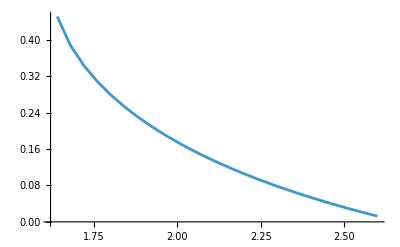

```mathematica
ListLinePlot[{mutinftb2},PlotRange->All]
```

```mathematica
a=1;
lvsuctb = {};
ucvsltb={};
For[i=0.00001,i≤0.81,i+=0.001,uc=i;
l=2*Quiet[NIntegrate[uc^3/(u^5 Sqrt[(1-(uc/u)^6)(1/(1+a^4 u^4))]),{u,uc,Infinity}]];
AppendTo[lvsuctb,{uc,l}];
AppendTo[ucvsltb,{l,uc}]
]
```

```mathematica
Clear[l]
ucvsl=Interpolation[ucvsltb]
```

InterpolatingFunction[…]

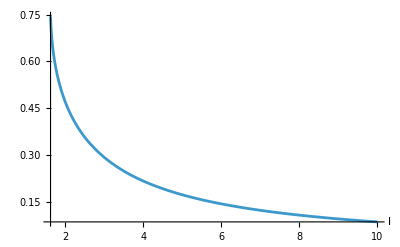

```mathematica
Plot[ucvsl[l],{l,1.62,10},PlotRange->All,AxesLabel->Automatic]
```

```mathematica
a=0.5;mutinfvsxtb={};
splinttb={};
spxinttb={};
sp2lxinttb={};
For[i=0,i≤0.8,i+=0.01,
l=4;
x=i*l;
uc=ucvsl[l];
ucx=ucvsl[x];
uc2lx=ucvsl[2l+x];
splint=2*Quiet[NIntegrate[u*Sqrt[(1+(a*u)^4)/(1-(uc/u)^6)],{u,uc,1000}]];
spxint=2*Quiet[NIntegrate[u*Sqrt[(1+(a*u)^4)/(1-(ucx/u)^6)],{u,ucx,1000}]];
sp2lxint=2*Quiet[NIntegrate[u*Sqrt[(1+(a*u)^4)/(1-(uc2lx/u)^6)],{u,uc2lx,1000}]];
mutinf=2*splint - sp2lxint - spxint;
AppendTo[mutinfvsxtb,{x,mutinf}];
]
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.04} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.08} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

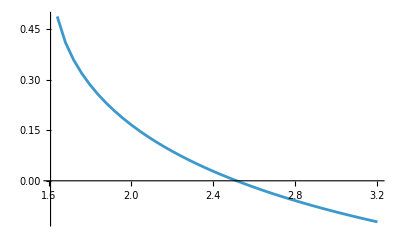

```mathematica
ListLinePlot[mutinfvsxtb]
```

```mathematica
mutinfvsxvsatb={};
For[a=0,a<=2,a+=0.1,
For[i=0.42,i≤0.8,i+=0.01,
l=4;
x=i*l;
uc=ucvsl[l];
ucx=ucvsl[x];
uc2lx=ucvsl[2l+x];
splint=2*SetPrecision[Quiet[NIntegrate[u*Sqrt[(1+(a*u)^4)/(1-(uc/u)^6)],{u,uc,1000}]],20];
spxint=2*SetPrecision[Quiet[NIntegrate[u*Sqrt[(1+(a*u)^4)/(1-(ucx/u)^6)],{u,ucx,1000}]],20];
sp2lxint=2*SetPrecision[Quiet[NIntegrate[u*Sqrt[(1+(a*u)^4)/(1-(uc2lx/u)^6)],{u,uc2lx,1000}]],20];
mutinf=Re[2*splint - sp2lxint - spxint];
AppendTo[mutinfvsxvsatb,{x,mutinf,a}];
]]
```

```mathematica
ListPointPlot3D[mutinfvsxvsatb,PlotRange->All,AxesLabel->{"x", "mutinf", "a"}]
```

-Graphics3D-

```mathematica
(*why the fuck is there a minimum at a~0.5??? things to check: maybe outside validity regime, maybe choice of integration limits, maybe machine precision (try python). this is inconsistent with figure 5, so im sure it's unphysical...*)
```

```mathematica
mutinfvsxvsatb
```

```mathematica
uc2=ucvsl[4]
```

0.216896

```mathematica
mutinfvsxtb2={};
mutinfvsxanductb={};
a=1;
l=10;
alpha=20;
splinttb={};
spxinttb={};
sp2lxinttb={};
For[i=1,i≤3,i+=0.01,
uc=ucvsl[l];
ucx=uc*i;
x=2*Quiet[NIntegrate[ucx^3/(u^5 Sqrt[(1-(ucx/u)^6)(1/(1+a^4 u^4))]),{u,ucx,Infinity}]];
uc2lx=ucvsl[2l+x];
splint=2*Quiet[NIntegrate[u*Sqrt[(1+(a*u)^4)/(1-(uc/u)^6)],{u,uc,alpha}]];
spxint=2*Quiet[NIntegrate[u*Sqrt[(1+(a*u)^4)/(1-(ucx/u)^6)],{u,ucx,alpha}]];
sp2lxint=2*Quiet[NIntegrate[u*Sqrt[(1+(a*u)^4)/(1-(uc2lx/u)^6)],{u,uc2lx,alpha}]];
mutinf=2*splint - sp2lxint - spxint;
AppendTo[mutinfvsxtb2,{x,mutinf}];
AppendTo[mutinfvsxanductb,{x,mutinf,ucx}];
]
```

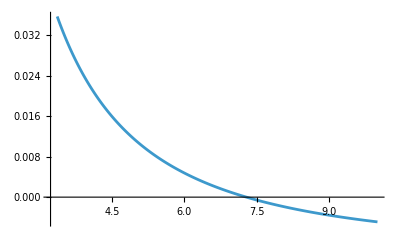

```mathematica
ListLinePlot[mutinfvsxtb2]
```

```mathematica
(*seriously why the fuck is there still a minimum below a=0?? going to be some stupid mistake fosho*)
(*ok so maybe, just maybe, setting the one interpolation function for a=1 and then changing a after is bas practice and that might be fuckin me up*)
```

```mathematica
(*Clear[k]
sptintegrand[y_,k_]=Normal[Series[y*Sqrt[(1+y^4)/(1-k^6/y^6)],{y,k,3}]];*)
```

```mathematica
ucvslinterp[a0_]:=Module[{a=a0,lvsuctb = {},ucvsltb={}},
For[i=0.001,i≤0.7991,i+=0.001,uc=i/a;
l=2*Quiet[NIntegrate[uc^3/(u^5 Sqrt[(1-(uc/u)^6)(1/(1+a^4 u^4))]),{u,uc,Infinity}]];
AppendTo[lvsuctb,{uc,l}];
AppendTo[ucvsltb,{l,uc}]
];
Clear[l];
Interpolation[ucvsltb]
]
```

```mathematica
ucvsl0=ucvslinterp[0.01];
```

```mathematica
ucvsl05=ucvslinterp[0.5];
ucvsl1=ucvslinterp[1];
ucvsl12=ucvslinterp[1.2];
ucvsl20=ucvslinterp[2];
```

```mathematica
ucvsl0plt=Plot[ucvsl0[l],{l,0.25*1.6138741919546127,10},PlotRange->All,PlotStyle->Orange];
ucvsl05plt=Plot[ucvsl05[l],{l,0.5*1.6138741919546127,10},PlotRange->All,PlotStyle->Dashed];
ucvsl1plt=Plot[ucvsl1[l],{l,1.6138741919546127,10},PlotRange->All,PlotStyle->Black];
ucvsl12plt=Plot[ucvsl12[l],{l,1.2*1.6138741919546127,10},PlotRange->All,PlotStyle->Blue];
ucvsl20plt=Plot[ucvsl20[l],{l,2*1.6138741919546127,10},PlotRange->All,PlotStyle->Red];
```

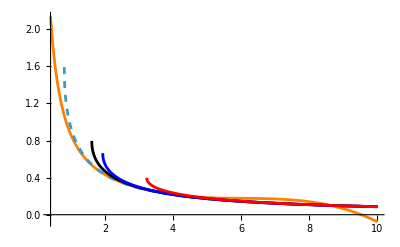

```mathematica
Show[{ucvsl0plt,ucvsl05plt,ucvsl1plt,ucvsl12plt,ucvsl20plt}]
```

```mathematica
mutinfvsxtb3={};
mutinfvsxanductb2={};
splinttb={};
spxinttb={};
sp2lxinttb={};
a=2;
alpha=500;
firstucfunc=ucvslinterp[a];
lc=a*1.6138741919546127;
lmult=4;
l=lc*lmult;
ucl=firstucfunc[l];
For[i=0,i≤0.5,i+=0.001,
x=lc+i*l;
ucx=firstucfunc[x];
uc2lx=firstucfunc[2l+x];
splint=2*Quiet[NIntegrate[u*Sqrt[(1+(a*u)^4)/(1-(ucl/u)^6)],{u,ucl,alpha}]];
spxint=2*Quiet[NIntegrate[u*Sqrt[(1+(a*u)^4)/(1-(ucx/u)^6)],{u,ucx,alpha}]];
sp2lxint=2*Quiet[NIntegrate[u*Sqrt[(1+(a*u)^4)/(1-(uc2lx/u)^6)],{u,uc2lx,alpha}]];
mutinf=2*splint - sp2lxint - spxint;
AppendTo[mutinfvsxtb3,{x,mutinf}];
AppendTo[mutinfvsxanductb2,{x,mutinf,ucx}];
]
```

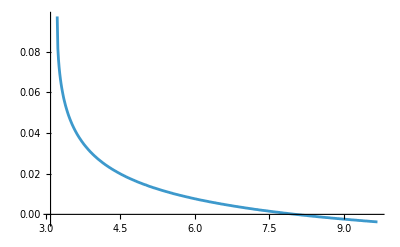

```mathematica
ListLinePlot[mutinfvsxtb3,PlotRange->All]
```

```mathematica
(*lets turn this into a nice lil function*)
```

```mathematica
mutinffunc[a0_,alpha_,lmult_]:=Module[{mutinfvsxtb={},a=a0},
firstucfunc=ucvslinterp[a];
lc=a*1.6138741919546127;
l=lc*lmult;
ucl=firstucfunc[l];
For[i=0,i≤0.5,i+=0.001,
x=lc+i*l;
ucx=firstucfunc[x];
uc2lx=firstucfunc[2l+x];
splint=2*Quiet[NIntegrate[u*Sqrt[(1+(a*u)^4)/(1-(ucl/u)^6)],{u,ucl,alpha}]];
spxint=2*Quiet[NIntegrate[u*Sqrt[(1+(a*u)^4)/(1-(ucx/u)^6)],{u,ucx,alpha}]];
sp2lxint=2*Quiet[NIntegrate[u*Sqrt[(1+(a*u)^4)/(1-(uc2lx/u)^6)],{u,uc2lx,alpha}]];
mutinf=2*splint - sp2lxint - spxint;
AppendTo[mutinfvsxtb,{x,mutinf}];
];
mutinfvsxtb
];
```

```mathematica
mutinftb15004=mutinffunc[1,500,4];
```

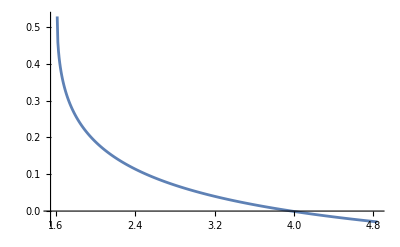

```mathematica
ListLinePlot[mutinftb15004]
```

```mathematica
(*alpha=1000;
sptaylor={};
For[i=0.1,i<=0.7,i+=0.01,k=i+0.01;
la=2*Quiet[NIntegrate[(k^3*Sqrt[1+y^4])/(y^2*Sqrt[y^6-k^6]),{y,k,alpha}]];
spt=2*(Quiet[NIntegrate[sptintegrand[y,k], {y,k,2.4*k}]]+Quiet[NIntegrate[y*Sqrt[(1+y^4)/(1-k^6/y^6)],{y,2.4*k,alpha}]]-((alpha)^4/4+Log[alpha]/2));
AppendTo[sptaylor,{la,spt}];
]*)
```

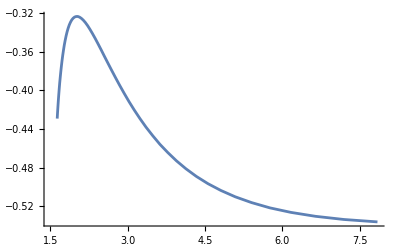

```mathematica
(*ListLinePlot[sptaylor,PlotRange->All]*)
```

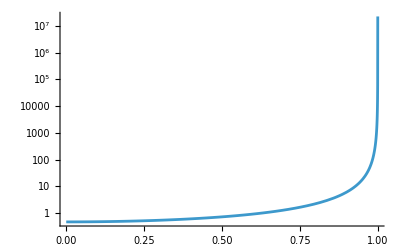

```mathematica
(*With[{k=1},LogPlot[k^2/(3(1-z^2)^(5/3))*Sqrt[(1-z^2)^(2/3)+k^4],{z,0,0.99999},PlotRange->All]]*)
```

```mathematica
(*Plot3D[y*Sqrt[(1+y^4)/(1-k^6/y^6)],{y,0.8,alpha},{k,0.8,200},ScalingFunctions->"Log",PlotRange->All,AxesLabel->Automatic]*)
```

-Graphics3D-